## Plot Kendall tau distributions of EWS in Ricker model

## Import data

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/fisheries/ktau_comp"];
```

```mathematica
dir="tmax1000_rw025";
```

```mathematica
ktauFold=Import["data_export/fold_"<>dir<>"/ktau.csv"];
ktauFlip=Import["data_export/flip_"<>dir<>"/ktau.csv"];
```

```mathematica
(* number of entries *)
{Length[ktauFold],Length[ktauFlip]}
```

{101,101}

## Box-whisker plots

```mathematica
(* figure parameters *)
imgs=300;
padding={{60,30},{50,40}};
aratio=1;
```

```mathematica
(* index values *)
ews={"Variance","Smax","Lag-1 AC","Lag-2 AC"};
index=Table[Position[ktauFold[[1]],ews[[i]]],{i,1,Length[ews]}]//Flatten;
```

```mathematica
(* Fold bifurcation *)
plotFold=BoxWhiskerChart[Transpose[ktauFold[[2;;,index]]],"Outliers",
PlotRange->{All,{-1,1}},
FrameTicks->{{Automatic,None},{Automatic,None}},
ImageSize->imgs,
Frame->True,
LabelStyle->14,
ChartStyle->Lighter[TMBcolours[[1]],0.2],
ChartLabels->{"Var","S_max","AC(1)","AC(2)"},
GridLines->{None,Range[-1,1,0.5]},
ImagePadding->padding,
AspectRatio->aratio,
FrameLabel->{{"Kendall tau",None},{"EWS",Style["Fold bifurcation",Bold]}}];
```

```mathematica
(* Flip bifurcation *)
plotFlip=BoxWhiskerChart[Transpose[ktauFlip[[2;;,index]]],"Outliers",
PlotRange->{All,{-1,1}},
FrameTicks->{{Automatic,None},{Automatic,None}},
ImageSize->imgs,
Frame->True,
LabelStyle->14,
ChartStyle->Lighter[TMBcolours[[1]],0.2],
ChartLabels->{"Var","S_max","AC(1)","AC(2)"},
GridLines->{None,Range[-1,1,0.5]},
ImagePadding->padding,
AspectRatio->aratio,
FrameLabel->{{"Kendall tau",None},{"EWS",Style["Flip bifurcation",Bold]}}];
```

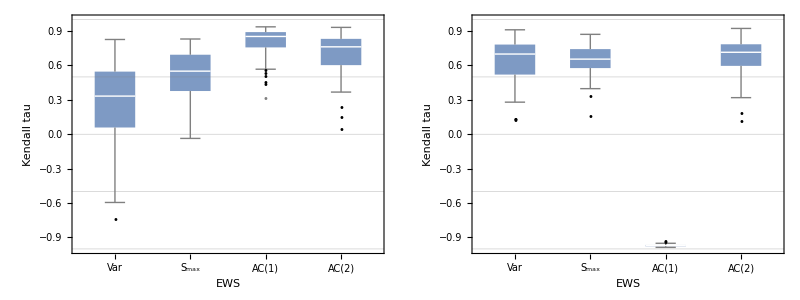

```mathematica
plotComb=Grid[{{plotFold,plotFlip}}]
```

```mathematica
(* Export plot *)
Export["figures/"<>dir<>".png",plotComb];
```